## Figure 3(Asymmetry in conditioning ability and niche width)

### Setup

```mathematica
f[a_,b_,v_,p_,q_]:= v NIntegrate[Exp[(-(x-p)^2)/a^2]Exp[(-(x-q)^4)/(81 b^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x-p)^2)/a^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]=Subscript[N, 1](1-S^4/Subscript[ω, 1]^4-(Subscript[α, 11] Subscript[N, 1]+Subscript[α, 12] Subscript[N, 2]))
Subscript[dN, 2]=Subscript[N, 2](1-(S-ϵ)^4/Subscript[ω, 2]^4-(Subscript[α, 21] Subscript[N, 1]+Subscript[α, 22] Subscript[N, 2]))
dS=Subscript[η, 1](-S)Subscript[N, 1]+Subscript[η, 2](ϵ-S)Subscript[N, 2];
```

N_1 (1-N_1 α_11-N_2 α_12-S^4/ω_1^4)

N_2 (1-N_1 α_21-N_2 α_22-(S-ϵ)^4/ω_2^4)

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

### Symmetric case for reference (same as Figure 2c)

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
multiCoex=0;
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{44.2969,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,1619,0,272,0,0}

```mathematica
multiCoex
```

0

#### Result

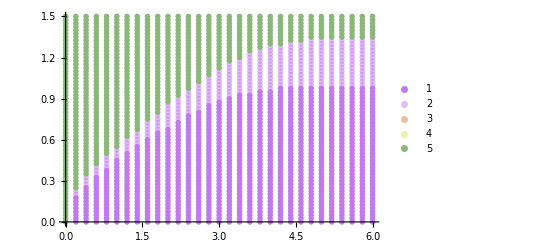

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

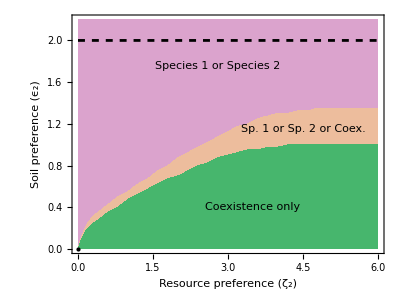

```mathematica
Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,2.2},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],Plot[(Subscript[ω, 1]+Subscript[ω, 2])/.pars,{ζ,0,6},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{2.8,1.75}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->13]],{4.5,1.15}],Inset[Text[Style["Coexistence only ",FontSize->13]],{3.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1Sym=z1;
z2Sym=z2;
```

### Figure 4a (Asymmetry in η)

#### Species 2 is much worse η_1=1, η_2=0.5

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->0.5};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]≥0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch1==1&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{98.7188,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,1856,0,35,0,0}

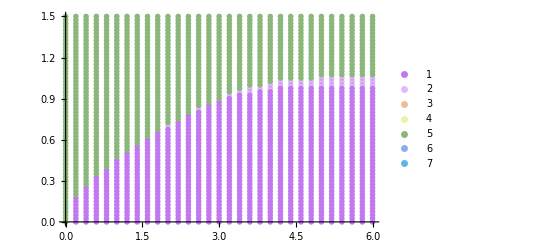

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z3];
```

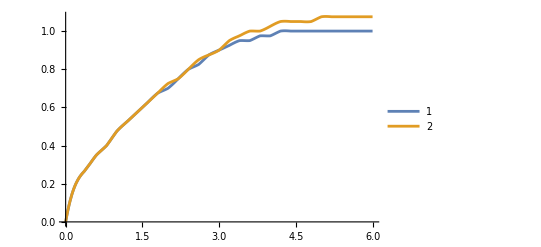

```mathematica
Plot[{f1[x],f2[x]},{x,0,6},PlotLegends->Automatic]
```

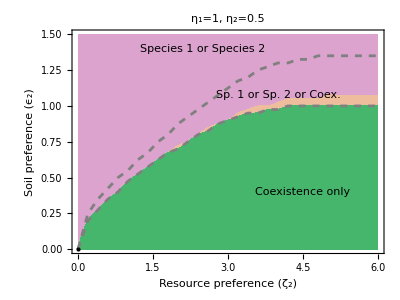

```mathematica
fig4a0=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=0.5",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{2.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->18]],{4,1.075}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4a0.jpg",fig4a0];
```

```mathematica
z1a0=z1;
z2a0=z3;
```

#### Species 2 is worse η_1=1, η_2=0.8

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->0.8};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch20=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]≥0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch1==1&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{76.1094,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,2180,0,176,0,0}

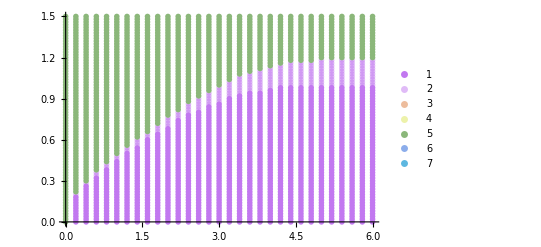

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z3];
```

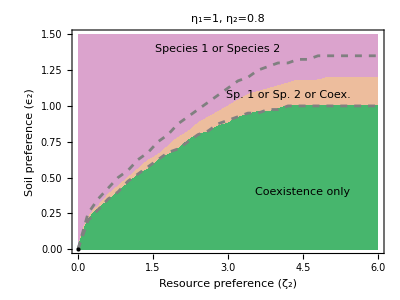

```mathematica
fig4a1=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=0.8",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{2.8,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->18]],{4.2,1.075}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4a1.jpg",fig4a1];
```

```mathematica
z1a1=z1;
z2a1=z3;
```

#### Species 2 is better η_1=1, η_2=1.5

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1.5};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]≥0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch1==1&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{36.875,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,2247,0,109,0,0}

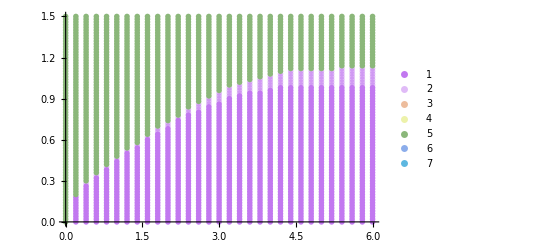

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z3];
```

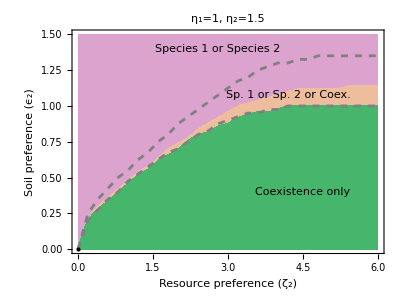

```mathematica
fig4a2=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=1.5",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{2.8,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->18]],{4.2,1.075}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4a2.jpg",fig4a2];
```

```mathematica
z1a2=z1;
z2a2=z3;
```

#### Species 2 is much better η_1=1, η_2=2

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->2};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]]<0,Print[{j1,j2,eq[[j1,j2]],Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]}]]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}];
λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}];
λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]>=0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]≥0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch1==1&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{96.3281,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,1856,0,35,0,0}

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

-Graphics-

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z3];
```

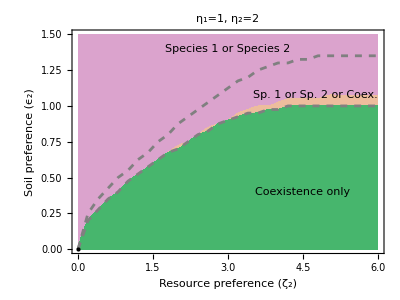

```mathematica
fig4a3=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],ListLinePlot[{z1Sym,z2Sym},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["η_1=1, η_2=2",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.75,1.075}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4a3.jpg",fig4a3];
```

```mathematica
z1a2=z1;
z2a2=z3;
```

#### Summary

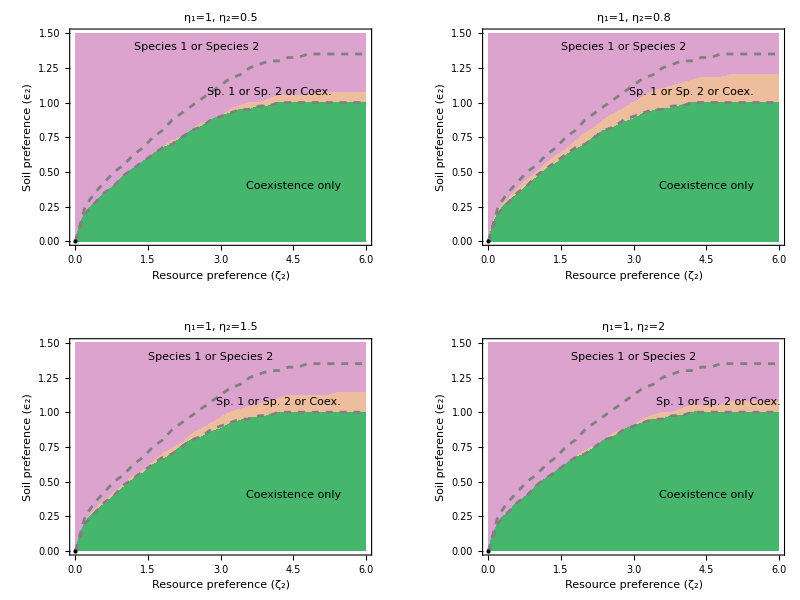

```mathematica
GraphicsGrid[{{fig4a0,fig4a1},{fig4a2,fig4a3}},ImageSize->800]
```

### Figure 4b (Asymmetry in ω)

#### Species 2 is much worse ω_1=1, ω_2=0.7

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->0.7,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
multiCoex=0;
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
If[Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch1==1&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{114.719,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{129,1607,155,0,0,0}

```mathematica
multiCoex
```

0

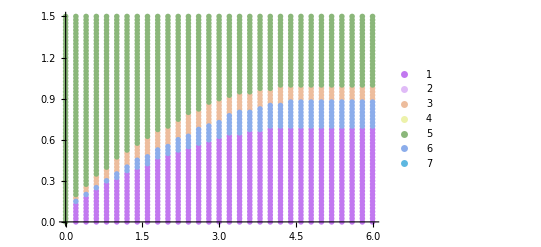

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

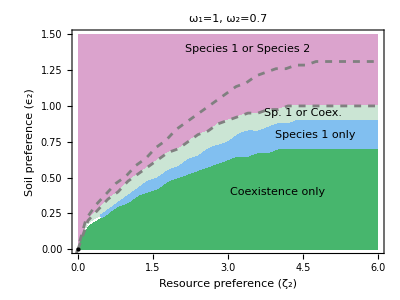

```mathematica
fig4b0=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f1[x]<y<f2[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[Rational[43, 85], Rational[191, 255], Rational[16, 17]]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ω_1=1, ω_2=0.7",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{3.4,1.4}],Inset[Text[Style["Sp. 1 or Coex.",FontSize->18]],{4.5,0.95}],Inset[Text[Style["Species 1 only",FontSize->18]],{4.75,0.8}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4b0.jpg",fig4b0];
```

```mathematica
z1b0=z1;
z2b0=z2;
z3b0=z3;
```

#### Species 2 is worse ω_1=1, ω_2=0.9

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->0.9,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
multiCoex=0;
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
If[Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ=Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]];
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{123.516,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,2093,115,148,0,0}

```mathematica
multiCoex
```

0

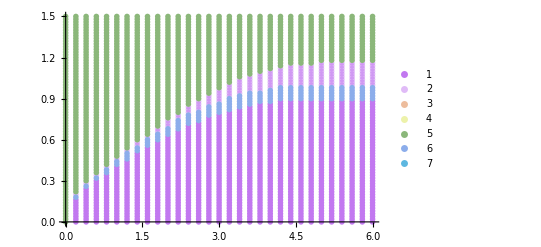

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
RGBColor[129/255,191/255,240/255]
```

RGBColor[Rational[43, 85], Rational[191, 255], Rational[16, 17]]

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

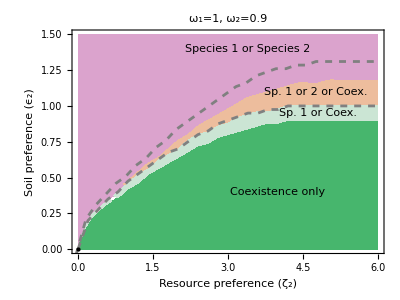

```mathematica
fig4b1=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f3[x]<y<f2[x],f1[x]<y<f2[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[Rational[43, 85], Rational[191, 255], Rational[16, 17]],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->8],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ω_1=1, ω_2=0.9",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{3.4,1.4}],Inset[Text[Style["Sp. 1 or Coex. ",FontSize->15]],{4.8,0.95}],Inset[Text[Style["Sp. 1 or 2 or Coex. ",FontSize->15]],{4.75,1.1}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4b1.jpg",fig4b1];
```

```mathematica
z1b1=z1;
z2b1=z2;
z3b1=z3;
```

#### Species 2 is better ω_1=1, ω_2=1.1

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
multiCoex=0;
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
ch4=0;
ch5=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ2[[j1,j2]]<0&&ch1==1&& ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{126.438,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,2065,114,177,0,0}

```mathematica
multiCoex
```

0

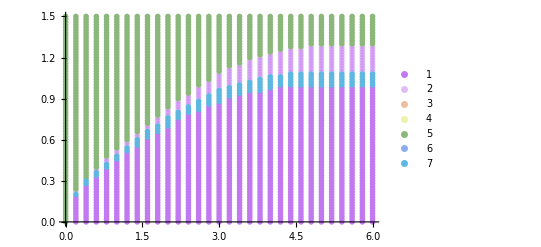

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

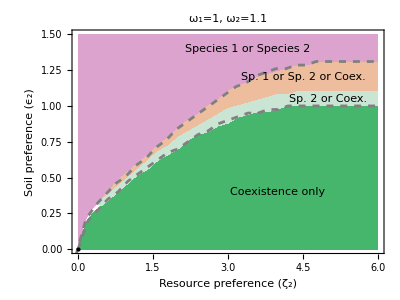

```mathematica
fig4b2=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f1[x]<y<f2[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ω_1=1, ω_2=1.1",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3.4,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->15]],{4.5,1.2}],Inset[Text[Style["Sp. 2 or Coex. ",FontSize->15]],{5,1.05}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4b2.jpg",fig4b2];
```

```mathematica
z1b2=z1;
z2b2=z2;
z3b2=z3;
```

#### Species 2 is much better ω_1=1, ω_2=1.4

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.4,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
multiCoex=0;
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
ch4=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ2[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch4==0,z4[[j1]]={ζs[[j1]],ϵs[[j2]]};ch4=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{64.3438,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{153,1518,220,0,0,0}

```mathematica
multiCoex
```

0

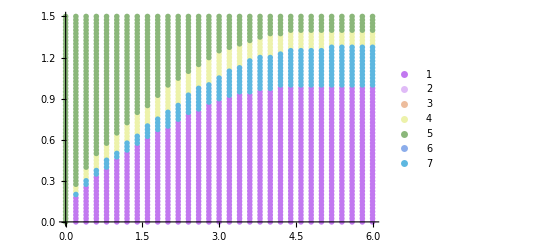

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
f4=Interpolation[z4];
```

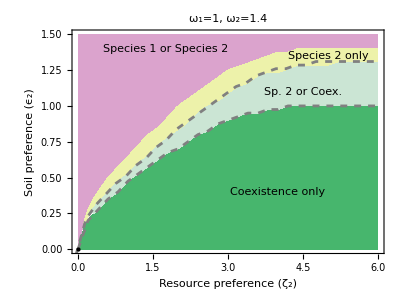

```mathematica
fig4b3=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f4[x]<y<f3[x],f1[x]<y<f4[x]&&y<f2[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.929162, 0.95034, 0.6648153333333333],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ω_1=1, ω_2=1.4",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{1.75,1.4}],Inset[Text[Style["Sp. 2 or Coex. ",FontSize->18]],{4.5,1.1}],Inset[Text[Style["Species 2 only",FontSize->15]],{5,1.35}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4b3.jpg",fig4b3];
```

```mathematica
z1b3=z1;
z2b3=z2;
z3b3=z4;
```

#### Summary

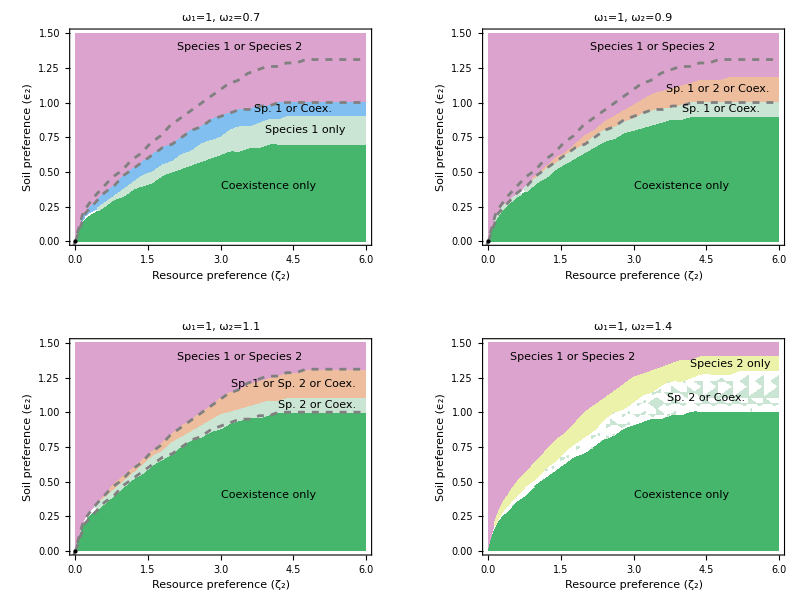

```mathematica
GraphicsGrid[{{fig4b0,fig4b1},{fig4b2,fig4b3}},ImageSize->800]
```

### Figure 4c (Asymmetry in σ)

#### Species 2 is much worse σ_1=1, σ_2=0.6

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->0.6,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{219.594,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{602,3653,36,345,0,0}

```mathematica
multiCoex
```

0

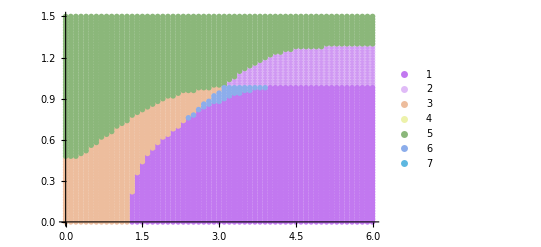

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

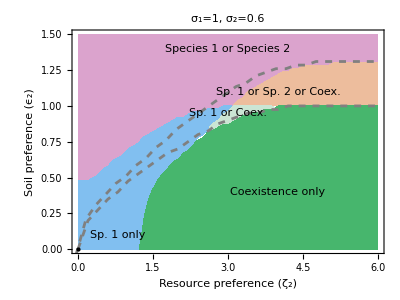

```mathematica
fig4c0=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f3[x]<y<f2[x],f1[x]<y<f2[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[Rational[43, 85], Rational[191, 255], Rational[16, 17]],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["σ_1=1, σ_2=0.6",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->18]],{4,1.1}],Inset[Text[Style["Sp. 1 or Coex.",FontSize->15]],{3,0.95}],Inset[Text[Style["Sp. 1 only",FontSize->15]],{0.8,0.1}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1c0=z1;
z2c0=z2;
z3c0=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4c0.jpg",fig4c0];
```

#### Species 2 is worse σ_1=1, σ_2=0.8

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->0.8,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{227.875,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{285,3911,49,391,0,0}

```mathematica
multiCoex
```

0

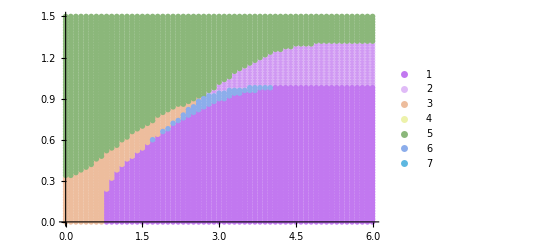

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

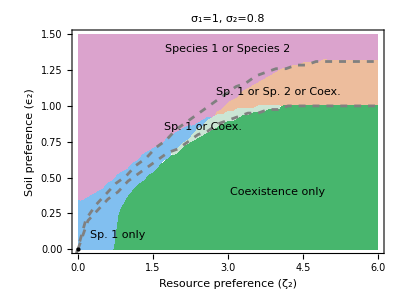

```mathematica
fig4c1=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f3[x]<y<f2[x],f1[x]<y<f2[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[Rational[43, 85], Rational[191, 255], Rational[16, 17]],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["σ_1=1, σ_2=0.8",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->18]],{4,1.1}],Inset[Text[Style["Sp. 1 or Coex.",FontSize->15]],{2.5,0.85}],Inset[Text[Style["Sp. 1 only",FontSize->15]],{0.8,0.1}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1c1=z1;
z2c1=z2;
z3c1=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4c1.jpg",fig4c1];
```

#### Species 2 is better σ_1=1, σ_2=1.2

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1.2,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ2[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{120.828,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{228,4055,63,290,0,0}

```mathematica
multiCoex
```

0

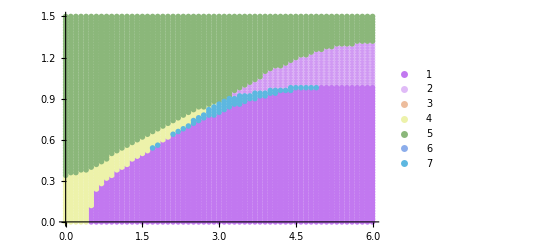

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

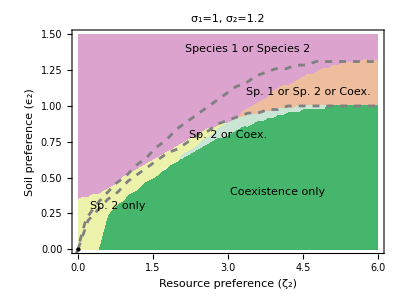

```mathematica
fig4c2=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f3[x]<y<f2[x],f1[x]<y<f2[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.929162, 0.95034, 0.6648153333333333],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["σ_1=1, σ_2=1.2",FontSize->18],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->18,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->15]],{3.4,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->15]],{4.6,1.1}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->15]],{3,0.8}],Inset[Text[Style["Sp. 2 only",FontSize->15]],{0.8,0.3}],Inset[Text[Style["Coexistence only ",FontSize->15]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1c2=z1;
z2c2=z2;
z3c2=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4c2.jpg",fig4c2];
```

#### Species 2 is much better σ_1=1, σ_2=1.5

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1.5,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ3[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ2[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{224.188,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{573,3890,65,108,0,0}

```mathematica
multiCoex
```

0

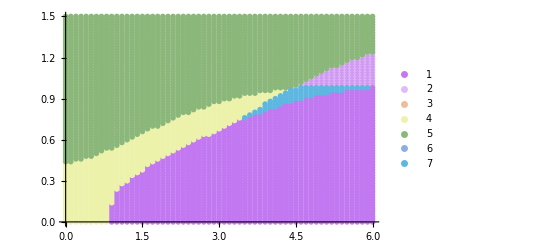

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

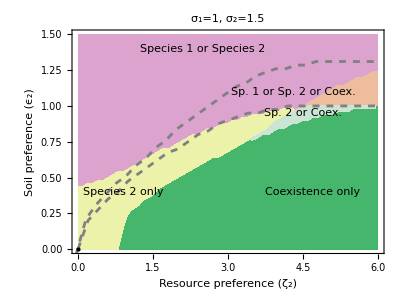

```mathematica
fig4c3=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f3[x]<y<f2[x],f1[x]<y<f2[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.929162, 0.95034, 0.6648153333333333],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["σ_1=1, σ_2=1.5",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{2.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->15]],{4.3,1.1}],Inset[Text[Style["Sp. 2 or Coex.",FontSize->15]],{4.5,0.95}],Inset[Text[Style["Species 2 only",FontSize->15]],{0.9,0.4}],Inset[Text[Style["Coexistence only ",FontSize->17]],{4.7,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1c3=z1;
z2c3=z2;
z3c3=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\fig4c3.jpg",fig4c3];
```

#### Summary

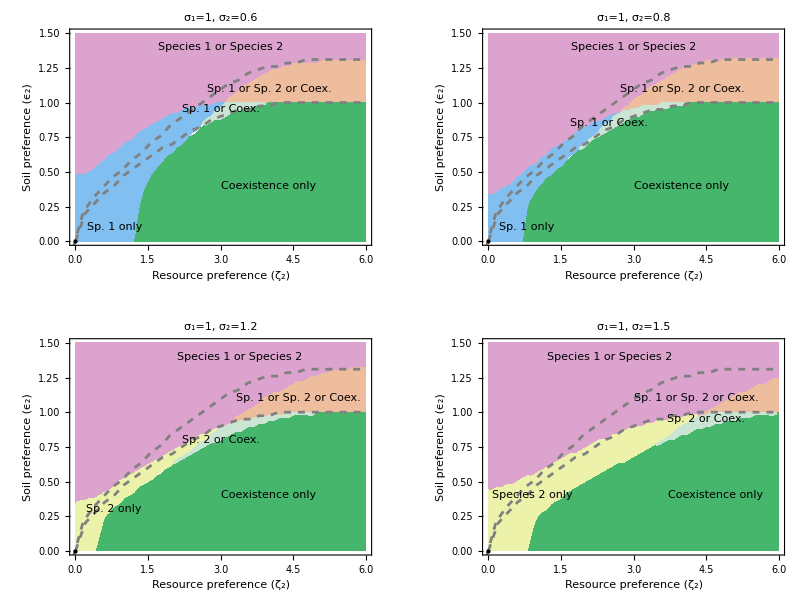

```mathematica
GraphicsGrid[{{fig4c0,fig4c1},{fig4c2,fig4c3}},ImageSize->800]
```

## Appendix A8

### No PSF

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->0,Subscript[η, 2]->0};
ϵs=Range[0,1.5,0.05];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf","α","α_12","α_21"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

#### Result

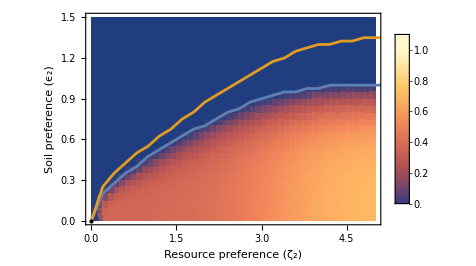

```mathematica
figA7a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

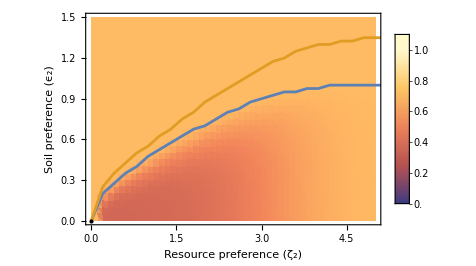

```mathematica
figA7b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA7a.jpg",figA7a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA7b.jpg",figA7b];
```

### Symmetric invader

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.01];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

#### Result

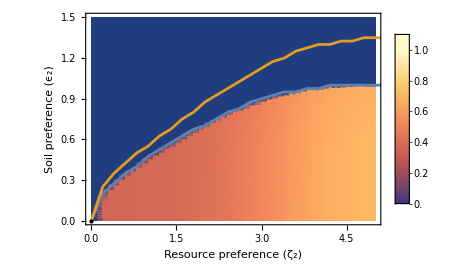

```mathematica
figA8a=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

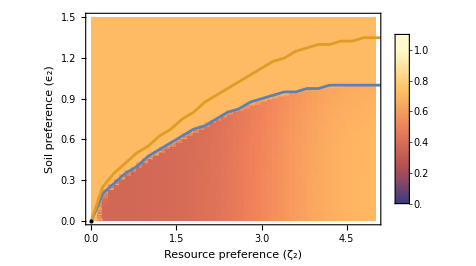

```mathematica
figA8b=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1Sym,z2Sym}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA8a.jpg",figA8a];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA8b.jpg",figA8b];
```

### Asymmetry in conditioning

#### Weakly conditioning invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->0.8};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Timing[
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
]
```

{173.25,Null}

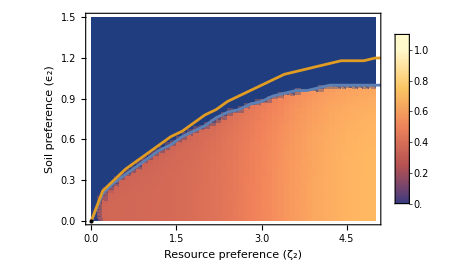

```mathematica
figA9a0=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1a1,z2a1}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

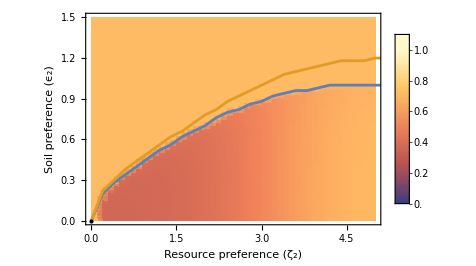

```mathematica
figA9b0=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1a1,z2a1}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA9a.jpg",figA9a0];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA9b.jpg",figA9b0];
```

#### Strongly conditioning invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1.5};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Timing[
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
]
```

{180.531,Null}

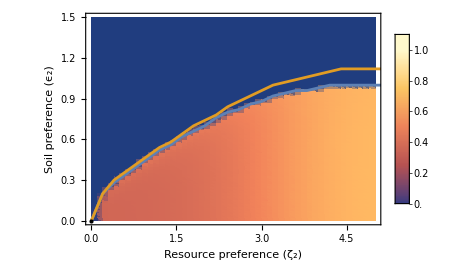

```mathematica
figA9a1=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1a2,z2a2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

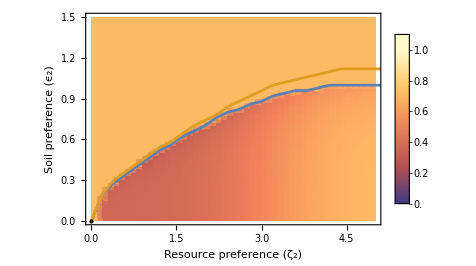

```mathematica
figA9b1=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1a2,z2a2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA9a1.jpg",figA9a1];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA9b1.jpg",figA9b1];
```

### Asymmetry in soil niche width

#### Very intolerant invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->0.7,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

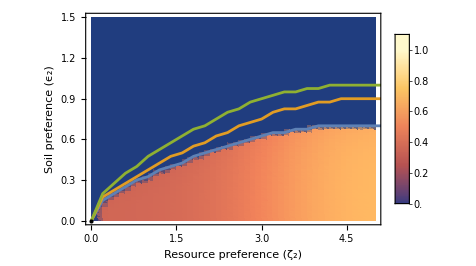

```mathematica
Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b0,z2b0,z3b0}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

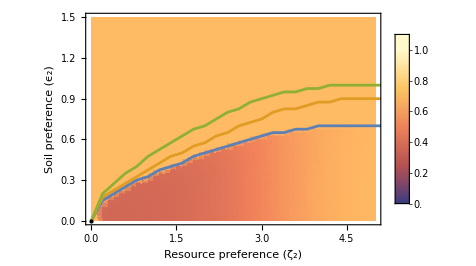

```mathematica
Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b0,z2b0,z3b0}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

#### Intolerant invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->0.9,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

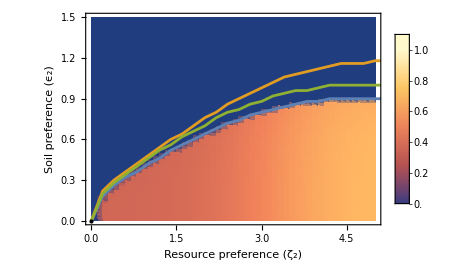

```mathematica
Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b1,z2b1,z3b1}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

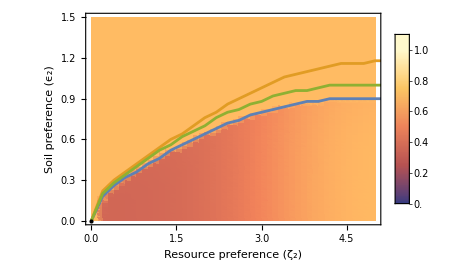

```mathematica
Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b1,z2b1,z3b1}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

#### Tolerant invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

```mathematica
Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b2,z2b2,z3b2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b2,z2b2,z3b2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

#### Very tolerant invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1.4,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

```mathematica
figA10a1=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b3,z2b3,z3b3}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
figA10b1=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1b3,z2b3,z3b3}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA10a1.jpg",figA10a1];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA10b1.jpg",figA10b1];
```

### Asymmetry in resource niche width

#### Very specialized invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->0.6,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

```mathematica
figA11a0=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c0,z2c0,z3c0}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
figA11b0=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c0,z2c0,z3c0}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\figA11a0.pdf",figA11a0];
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\figA11b0.pdf",figA11b0];
```

#### Specialized invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->0.8,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

```mathematica
figA11a1=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c1,z2c1,z3c1}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
figA11b1=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c1,z2c1,z3c1}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\figA11a1.pdf",figA11a1];
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\figA11b1.pdf",figA11b1];
```

#### Generalist invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1.2,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

```mathematica
figA11a2=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c2,z2c2,z3c2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
figA11b2=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1c2,z2c2,z3c2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

-Graphics-

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA11a2.jpg",figA11a2];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA11b2.jpg",figA11b2];
```